```mathematica
stirling[n_]:=√(2π n)(n/ⅇ)^n
```

```mathematica
Limit[(n!)/stirling[n],n->∞]
```

1

```mathematica
βnBaseβnChoosen=Assuming[
{β>1,n≥0},
(stirling[β n]/(stirling[n]stirling[β n-n])/((√β)/(√(2π n(β-1)))))^(1/(β n))//FullSimplify]
```

(-1+β)^(-1+1/β) β

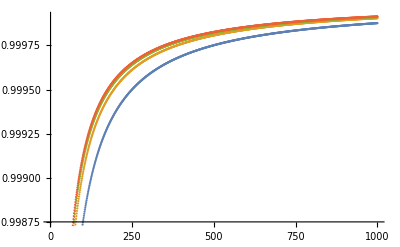

```mathematica
DiscretePlot[
Evaluate@Table[Binomial[β n,n]/(stirling[β n]/(stirling[n]stirling[β n-n])),{β,2,5}],
{n,1,1000},Filling->None]
```

```mathematica
bc[n_,k_]:=f[n]/(f[k]f[n-k])
```

```mathematica
c[n_]:=1/(n+1)bc[2n,n]
```

```mathematica
spc[k_,l_]:=(f[k+l](k-l+1))/(f[l]f[k+1])
```

```mathematica
(c[k]spc[k,l]/.(f[1+k]->(1+k)f[k]))/bc[k+l,k]
```

((1+k-l) f[2 k])/((1+k)^2 f[k]^2)

```mathematica
chvar=Solve[{n==k+l,l==α k,k+l==β k},{k,l,β}]⟦1⟧
```

{k→n/(1+α),l→(n α)/(1+α),β→1+α}

```mathematica
(spc[k,l]/.(f[1+k]->(1+k)f[k]))/bc[k+l,k]/.chvar//Simplify
```

(1+n+α-n α)/(1+n+α)

```mathematica
spcContribution=βnBaseβnChoosen/.chvar
```

α^(-1+1/(1+α)) (1+α)

```mathematica
-1+1/(1+α)//Together
```

-α/(1+α)

```mathematica
catalanContribution=4^(k/n)/.chvar
```

4^(1/(1+α))

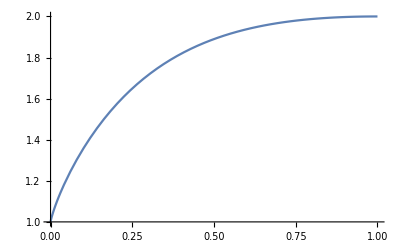

```mathematica
Plot[spcContribution,{α,0,1}]
```

```mathematica
catalanContribution spcContribution
```

4^(1/(1+α)) α^(-1+1/(1+α)) (1+α)

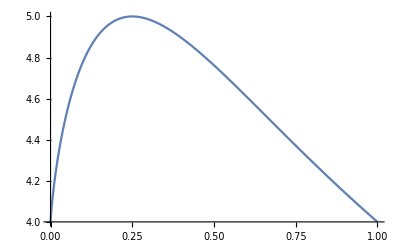

```mathematica
Plot[catalanContribution spcContribution,{α,0,1}]
```

```mathematica
{#,catalanContribution spcContribution/.#}&[Solve[{D[catalanContribution spcContribution,α]==0},{α}]⟦1⟧]//TableForm
```

α→1/4
5

```mathematica
Assuming[{k>0,l>0},catalanContribution spcContribution/.α->l/k//FullSimplify]
```

(4^(k/(k+l)) (l/k)^(k/(k+l)) (k+l))/l

```mathematica
Table[Table[spc[k,l]/.f->Factorial,{l,0,k}],{k,0,10}]//TableForm
```

1 |  |  |  |  |  |  |  |  |  | 
1 | 1 |  |  |  |  |  |  |  |  | 
1 | 2 | 2 |  |  |  |  |  |  |  | 
1 | 3 | 5 | 5 |  |  |  |  |  |  | 
1 | 4 | 9 | 14 | 14 |  |  |  |  |  | 
1 | 5 | 14 | 28 | 42 | 42 |  |  |  |  | 
1 | 6 | 20 | 48 | 90 | 132 | 132 |  |  |  | 
1 | 7 | 27 | 75 | 165 | 297 | 429 | 429 |  |  | 
1 | 8 | 35 | 110 | 275 | 572 | 1001 | 1430 | 1430 |  | 
1 | 9 | 44 | 154 | 429 | 1001 | 2002 | 3432 | 4862 | 4862 | 
1 | 10 | 54 | 208 | 637 | 1638 | 3640 | 7072 | 11934 | 16796 | 16796

```mathematica
(√β)/(√(2π n(β-1)))/.chvar
```

(√(1+α))/(√(2 π) √(n α))

```mathematica
βPlusOnenBaseβnChoosen=Assuming[
{β>1,n≥0},
((stirling[β n]/(stirling[n]stirling[β n-n])/((√β)/(√(2π n(β-1)))))^(1/n)//FullSimplify)^(1/(β+1))]
```

((-1+β)^(1-β) β^β)^(1/(1+β))

```mathematica
binomialFactor=βPlusOnenBaseβnChoosen/.β->1/α
```

((-1+1/α)^(1-1/α) (1/α)^(1/α))^(1/(1+1/α))

```mathematica
Assuming[{α≥0,α≤1},FullSimplify[binomialFactor]]
```

((1-α)^(1-1/α)/α)^(α/(1+α))

```mathematica
dbinomial=Assuming[{α≥0,α≤1},FullSimplify[D[binomialFactor,α]]];
```

```mathematica
Solve[dbinomial==0,α]
```

{{α→1/2 (3-√5)},{α→1/2 (3+√5)}}

```mathematica
binomialFactor/.α->1/2 (3-√5)//Simplify
```

1/2 (1+√5)

```mathematica
(binomialFactor/.α->1/2 (3-√5))==GoldenRatio//Simplify
```

True

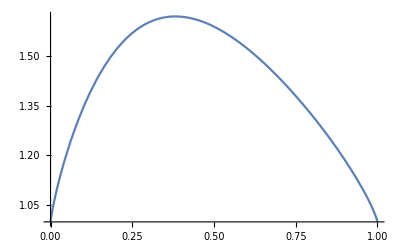

```mathematica
Plot[binomialFactor,{α,0,1}]
```

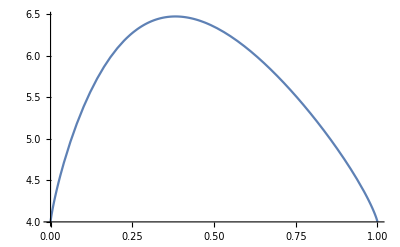

```mathematica
Plot[4binomialFactor,{α,0,1}]
```

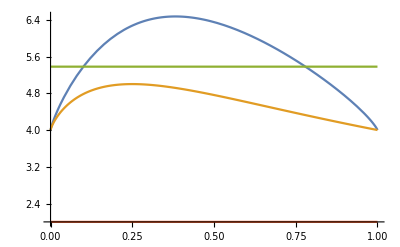

```mathematica
Plot[{4binomialFactor,catalanContribution spcContribution,2^(7/10)3^(-3/20)7^(7/10),2},{α,0,1}]
```

```mathematica
4GoldenRatio//N
```

6.47214